# Filter Function of Pulses

## Gabriel Patenotte, 11/3/22

See the oneNote in NaCs 1.5 2022: ‘noise filter results’
Reference:
Green, T. J., Strawman, J., Uys, H. & Biercuk, M. J. Arbitrary quantum control of qubits in the presence of universal noise. New J Phys 15, 095004 (2013).

### Parameters

```mathematica
Ω=.;tMax=.;pulseList=xy8;τ=.
```

### Background code

#### Pulses

{angle of rotation, vector of rotation or time of rotation}
vector of rotation = {x, y, z}

```mathematica
ramsey={{0,τ}};
wait={{0,τ}};
spinEcho={{0,τ},{π,"y"},{0,τ}};
piPulse={{π,"x"}};
bb1[θ_,ϕ_]:={{π,{Cos[ϕ+ArcCos[-θ/(4π)]],Sin[ϕ+ArcCos[-θ/(4π)]],0}},{2π,{Cos[ϕ+3ArcCos[-θ/(4π)]],Sin[ϕ+3ArcCos[-θ/(4π)]],0}},{π,{Cos[ϕ+ArcCos[-θ/(4π)]],Sin[ϕ+ArcCos[-θ/(4π)]],0}},{θ,{Cos[ϕ],Sin[ϕ],0}}}//.{"x"->0,"y"->π/2,"-x"->π,"-y"->(3π)/2}
xy8={{π,"x"},{0,2τ},{π,"y"},{0,2τ},{π,"x"},{0,2τ},{π,"y"},{0,2τ},{π,"y"},{0,2τ},{π,"x"},{0,2τ},{π,"y"},{0,2τ},{π,"x"},{0,τ}};
x8={{π,"x"},{0,τ},{π,"x"},{0,τ},{π,"x"},{0,τ},{π,"x"},{0,τ},{π,"x"},{0,τ},{π,"x"},{0,τ},{π,"x"},{0,τ},{π,"x"},{0,τ}};
xy16=Join[xy8[[;;-2]],{{0,τ}},xy8];
vecName={"x"->{1,0,0},"y"->{0,1,0},"z"->{0,0,1},"-x"->{-1,0,0},"-y"->{0,-1,0},"-z"->{0,0,-1}};
```

```mathematica
bb1[π,"x"]
```

{{π,{-1/4,(√15)/4,0}},{2 π,{Cos[3 ArcCos[-1/4]],Sin[3 ArcCos[-1/4]],0}},{π,{-1/4,(√15)/4,0}},{π,{1,0,0}}}

```mathematica
spinEchoBB1=Join[wait,bb1[π,"x"],wait];
```

#### Hamiltonians

```mathematica
σ={σx,σy,σz}=(PauliMatrix[#1]&)/@{1,2,3};σp=σx+ⅈ σy;σm=σx-ⅈ σy;
a=.;b=.;conj=Complex[a_,b_]->Complex[a,-b];
hc[x_]:=Transpose[x]/.conj;
Hc[vec_]:=If[SameQ[vec,0],({{0, 0}, {0, 0}}),1/2 Ω ∑_(n=1)^3 σ⟦n⟧ Normalize[vec]⟦n⟧]
```

#### Time Steps

```mathematica
findTime[pulse_]:=If[SameQ[pulse[[1]],0],{0,pulse[[2]]},{0,pulse[[1]]/Ω}]
findTimes[pulseList_]:=Accumulate[Flatten[findTime[pulseList[[#]]]&/@Range@Length[pulseList]]];
findτ0[pulseList_]:=If[!FreeQ[findTimes[pulseList][[-1]],τ],N[τ/.Solve[tMax==findTimes[pulseList][[-1]],τ]⟦1⟧],tMax]
```

#### Unitary matrices

```mathematica
Uc[t_,t0_,tf_,vec_]:=Simplify[MatrixExp[-ⅈ Hc[vec] Piecewise[{{t-t0,t0<t<tf},{tf-t0,t≥tf}}]],Assumptions->Ω>0];createUnitary[t_,pulseList_,τ0_:τ]:=Module[{tStarts,tEnds,vecs,tsI,vecName,pulses},
pulses=Length[pulseList];
vecName={"x"->{1,0,0},"y"->{0,1,0},"z"->{0,0,1},"-x"->{-1,0,0},"-y"->{0,-1,0},"-z"->{0,0,-1}};vecs=Replace[pulseList⟦All,2⟧/.vecName,i_/;Not[ListQ[i]]->0,1];
tsI=findTimes[pulseList];
tsI=tsI/.τ->τ0;Simplify[Dot@@Reverse[MapThread[Hold[Uc],{ConstantArray[t,pulses],tsI[[1;;;;2]],tsI⟦2;;;;2⟧,vecs}]]]]
```

```mathematica
findQ[pulseList_]:=Module[{Q,tFs},
Q={IdentityMatrix[2]};
tFs=findTimes[pulseList][[2;;;;2]];
Do[Q=Append[Q,If[Length[pulseList]==1,createUnitary[tFs[[n]],pulseList],Reverse[createUnitary[tFs[[n]],pulseList]]⟦n⟧].Q⟦-1⟧],{n,1,Length[pulseList]}];
Q]
```

```mathematica
Q=ReleaseHold[findQ[pulseList]];
Λ[i_,j_,l_]:=1/2 Tr[hc[Q[[l+1]]].σ[[i]].Q[[l+1]].σ[[j]]];
Λ[l_]:=Table[Λ[i,j,l],{i,1,3},{j,1,3}]
```

```mathematica
Rz[j_,l_,ω_]:=Module[{fl,gl,ti,tf,Ωl,θl,vec,σϕ},{ti,tf}=findTimes[pulseList][[2 l-1;;2l]];
vec=Replace[pulseList⟦l,2⟧/.vecName,i_/;Not[ListQ[i]]->{1,0,0}];
σϕ=Sum[vec[[n]]σ[[n]],{n,1,3}];
θl=pulseList[[l,1]];
Ωl=θl/(tf-ti);
fl=Exp[ⅈ ω (tf-ti)]Cos[θl]-1;
gl=Exp[ⅈ ω (tf-ti)]Sin[θl];
ω/(ω^2-Ωl^2)(KroneckerDelta[3,j](ⅈ Ωl gl-ω fl)+(Ωl fl-ⅈ ω gl)Tr[σϕ.σz.σ[[j]]])]
```

```mathematica
Rz[l_,ω_]:=Table[Rz[j,l,ω],{j,1,3}]
```

```mathematica
Rz[ω_]=Module[{tis},tis=findTimes[pulseList][[1;;;;2]];
Sum[Exp[ⅈ ω tis[[l]]](Rz[l,ω].Λ[l-1]),{l,1,Length@pulseList}]];
```

```mathematica
FzLim[ω_]=Total[((#/.conj)#)&/@Limit[Rz[ω],Ω->∞]];
```

```mathematica
Fz[ω_]=Total[((#/.conj)#)&/@Rz[ω]];
```

### Results

```mathematica
FullSimplify[FzLim[ω]]
```

4 (15-26 Cos[2 τ ω]+22 Cos[4 τ ω]-18 Cos[6 τ ω]+14 Cos[8 τ ω]-10 Cos[10 τ ω]+6 Cos[12 τ ω]-2 Cos[14 τ ω]) Sin[(τ ω)/2]^2

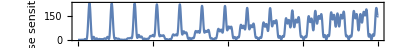

```mathematica
(*LogLinearPlot[FzLim[2π f]//.{τ->Limit[findτ0[pulseList],Ω->∞],tMax->1},{f,0,1000},PlotRange->All,Frame->True,FrameLabel->{"f","noise sensitivity"}]*)
Plot[Fz[2π f]//.{τ->findτ0[xy8],tMax->10 10^-3,Ω->π/(56.3 10^-6) },{f,0,10 10^3},PlotRange->All,Frame->True,FrameLabel->{"f","noise sensitivity"},AspectRatio->1/10,ImageSize->Full]
(*Plot[Fz[2π f]//.{τ->findτ0[spinEcho],tMax->1 10^-3,Ω->π/(56.3 10^-6) },{f,0,10 10^3},PlotRange->All,Frame->True,FrameLabel->{"f","noise sensitivity"},AspectRatio->1/10,ImageSize->Full]
Plot[Fz[2π f]//.{τ->findτ0[ramsey],tMax->1 10^-3,Ω->π/(56.3 10^-6) },{f,0,10 10^3},PlotRange->All,Frame->True,FrameLabel->{"f","noise sensitivity"},AspectRatio->1/10,ImageSize->Full]*)

(*Plot[FzLim[2π f]//.{τ->Limit[findτ0[pulseList],Ω->∞],tMax->1},{f,0,10},PlotRange->{0,125},Frame->True,FrameLabel->{"f","noise sensitivity"}]*)
```

```mathematica
findτ0[xy8]
```

(0.0666667 (-25.1327+tMax Ω))/Ω

```mathematica
τ/10^-3//.{τ->findτ0[pulseList],tMax->1.3*8 10^-3,Ω->π/(6.3 10^-6) }
```

0.689973

```mathematica
τ/10^-3//.{τ->findτ0[spinEcho],tMax->1.3 10^-3,Ω->π/(6.3 10^-6) }
```

0.64685

```mathematica
9.74/1.3
```

7.49231

```mathematica
1.3*7.5
```

9.75